# CalcPauliTransferEval

```mathematica
SetDirectory @ NotebookDirectory[];
Import["../Link/QuESTlink.m"];
```

## Doc

```mathematica
?CalcPauliTransferEval
```

## Correctness

## Maps

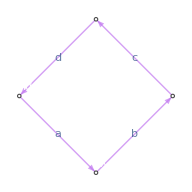

```mathematica
map = Subscript[PTMap, 0][0->{{1,a}},1->{{2,b}}, 2->{{3,c}}, 3->{{0,d}}];
DrawPauliTransferMap[map]
```

```mathematica
CalcPauliTransferEval[Subscript[X, 0], map];
Column @ MapAt[GetPauliString,%, {All,All,1}]
```

{{X_0,1,{{0,1}}}}
{{Y_0,2,{{1,b}}}}

```mathematica
CalcPauliTransferEval[Subscript[X, 0], {map,map,map}];
Column @ MapAt[GetPauliString,%, {All,All,1}]
```

{{X_0,1,{{0,1}}}}
{{Y_0,2,{{1,b}}}}
{{Z_0,3,{{2,c}}}}
{{Id_0,4,{{3,d}}}}

```mathematica
CalcPauliTransferEval[Subscript[X, 5], {map,map,map,map,map,map}];
Column @ MapAt[GetPauliString,%, {All,All,1}]
```

{{X_5,1,{{0,1}}}}
{{X_0 X_5,2,{{1,a}}}}
{{X_5 Y_0,3,{{2,b}}}}
{{X_5 Z_0,4,{{3,c}}}}
{{X_5,5,{{4,d}}}}
{{X_0 X_5,6,{{5,a}}}}
{{X_5 Y_0,7,{{6,b}}}}

## Circuits

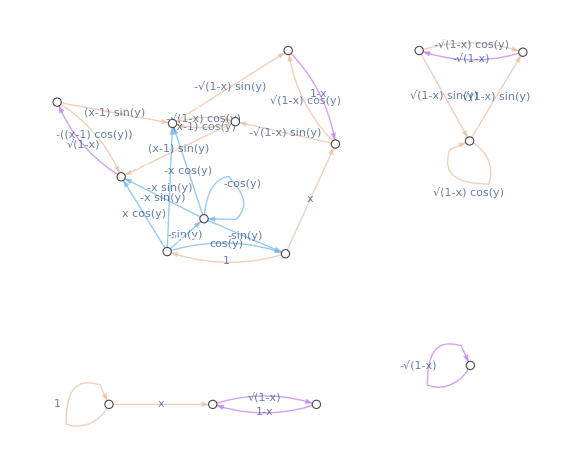

```mathematica
circ = Circuit[Subscript[H, 0] Subscript[H, 1] Subscript[Damp, 0][x] Subscript[Rx, 1][y] ];
DrawPauliTransferMap[circ]
```

```mathematica
CalcPauliTransferEval[ Subscript[Y, 0] Subscript[Y, 1], circ]
GetPauliString /@ %[[-1,All,1]]
```

{{{{2,2},1,{{0,1}}}},{{{2,2},2,{{1,-1}}}},{{{2,2},3,{{2,-1}}}},{{{2,2},4,{{3,√(1-x)}}}},{{{2,2},5,{{4,Cos[y]}}},{{3,2},6,{{4,Sin[y]}}}}}

{Y_0 Y_1,Y_0 Z_1}

```mathematica
CalcPauliTransferEval[ Subscript[Y, 1], circ];
GetPauliString /@ %[[-1,All,1]]

ApplyPauliTransferMap[Subscript[Y, 1],circ]
```

{Y_1,Z_1,Y_1 Z_0,Z_0 Z_1}

-Cos[y] Y_1-x Cos[y] Y_1 Z_0-Sin[y] Z_1-x Sin[y] Z_0 Z_1

```mathematica
repeated = Join @@ Table[circ,10];

CalcPauliTransferEval[ Subscript[Y, 1], repeated];
Plus @@ GetPauliString /@ %[[-1,All,1]]

(ApplyPauliTransferMap[Subscript[Y, 1],repeated] /. {x->.1,y->.15})[[All,2;;]]
```

X_1+X_0 X_1+Y_1+X_0 Y_1+X_1 Z_0+Y_1 Z_0+Z_1+X_0 Z_1+Z_0 Z_1

X_1+X_0 X_1+Y_1+X_0 Y_1+X_1 Z_0+Y_1 Z_0+Z_1+X_0 Z_1+Z_0 Z_1

## Options

### CombineStates

```mathematica
circ = Circuit[Subscript[H, 0] Subscript[H, 1] Subscript[Damp, 0][x] Subscript[Rx, 1][y] ];
circ = Join @@ Table[circ,5];

CalcPauliTransferEval[ Subscript[Y, 1], circ][[-1,All,1]]
Length[%]

CalcPauliTransferEval[ Subscript[Y, 1], circ, "CombineStates"->False][[-1,All,1]]
Length[%]
```

{{2,0},{3,0},{2,3},{3,3},{1,0},{1,3},{2,1},{3,1},{1,1}}

9

{{2,0},{3,0},{2,3},{3,3},{1,0},{1,3},{2,1},{3,1},{1,1},{2,0},{3,0},{2,3},{3,3},{2,1},{3,1},{2,3},{3,3},{1,3},{2,3},{3,3},{2,0},{3,0},{2,3},{3,3},{1,0},{1,3},{2,1},{3,1},{1,1},{2,3},{3,3},{1,3},{2,1},{3,1},{1,1},{2,1},{3,1},{2,1},{3,1},{1,1},{2,0},{3,0},{2,3},{3,3},{1,0},{1,3},{2,1},{3,1},{1,1},{2,0},{3,0},{2,3},{3,3},{2,1},{3,1},{2,3},{3,3},{1,3},{2,3},{3,3},{2,1},{3,1},{1,1},{2,1},{3,1},{2,3},{3,3},{1,3},{2,3},{3,3},{2,3},{3,3},{1,3},{2,3},{3,3},{1,3},{2,3},{3,3}}

78

```mathematica
history = CalcPauliTransferEval[ Subscript[Y, 1], circ];
ancestors = Flatten[history, 1][[All,3]];
Length /@ ancestors //Max

history = CalcPauliTransferEval[ Subscript[Y, 1], circ, "CombineStates"->False];
ancestors =Flatten[history, 1][[All,3]];
Length /@ ancestors //Max
```

2

1

### CacheMaps

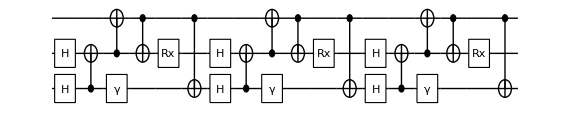

```mathematica
circ = Circuit[Subscript[H, 0] Subscript[H, 1] Subscript[C, 0][Subscript[X, 1]] Subscript[C, 1][Subscript[X, 2]]Subscript[Damp, 0][x] Subscript[C, 2][Subscript[X, 1]] Subscript[Rx, 1][y]Subscript[C, 2][Subscript[X, 0]] ];
circ = Join @@ Table[circ,3];
DrawCircuit[circ]
```

```mathematica
First @ Timing @ CalcPauliTransferEval[ Subscript[Y, 1], circ, "CacheMaps"->"Never"]
First @ Timing @ CalcPauliTransferEval[ Subscript[Y, 1], circ, "CacheMaps"->"UntilCallEnd"]
```

0.091459

0.017185

```mathematica
First @ Timing @ CalcPauliTransferEval[ Subscript[Y, 1], circ, "CacheMaps"->"Forever"]
First @ Timing @ CalcPauliTransferEval[ Subscript[Y, 1], circ, "CacheMaps"->"Forever"]
```

0.018647

0.003906

### AssertValidChannels

```mathematica
CalcPauliTransferEval[Subscript[Y, 2] Subscript[Y, 1] Subscript[Z, 0],Subscript[Damp, 0][x]]
CalcPauliTransferEval[Subscript[Y, 2] Subscript[Y, 1] Subscript[Z, 0],Subscript[Damp, 0][x], AssertValidChannels->False]
```

{{{{2,2,3},1,{{0,1}}}},{{{2,2,3},2,{{1,1-x}}}}}

{{{{2,2,3},1,{{0,1}}}},{{{2,2,0},2,{{1,1/2 (1-√(1-x) Conjugate[√(1-x)]-√x Conjugate[√x])}}},{{2,2,3},3,{{1,1/2 (1+√(1-x) Conjugate[√(1-x)]-√x Conjugate[√x])}}}}}

## Errors

```mathematica
CalcPauliTransferEval[Subscript[Id, 1],Subscript[PTMap, 2][{eh}]]
```

CalcPauliTransferEval::error: Could not pre-compute the Pauli transfer maps due to the below error:

CalcPauliTransferMatrix::error: Circuit contained an unrecognised or unsupported gate: PTMap_0[{eh}]

$Failed

```mathematica
CalcPauliTransferEval[Subscript[Id, 1],Subscript[Bop, 0]]
```

CalcPauliTransferEval::error: Could not pre-compute the Pauli transfer maps due to the below error:

CalcPauliTransferMatrix::error: Circuit contained an unrecognised or unsupported gate: Bop_0

$Failed

```mathematica
CalcPauliTransferEval[Subscript[Id, -1],Subscript[H, 0]]
```

CalcPauliTransferEval::error: Invalid arguments. See ?CalcPauliTransferEval

$Failed

```mathematica
CalcPauliTransferEval[1,Subscript[H, 0]]
```

CalcPauliTransferEval::error: Invalid arguments. See ?CalcPauliTransferEval

$Failed

```mathematica
CalcPauliTransferEval[Subscript[X, 0],Subscript[X, 0], "CacheMaps"->"x"]
```

CalcPauliTransferEval::error: Option "CacheMaps" must be one of "Forever", "UntilCallEnd" or "Never".

$Failed

```mathematica
CalcPauliTransferEval[Subscript[X, 0],Subscript[X, 0], "CombineStates"->"x"]
```

CalcPauliTransferEval::error: Option "CombineStates" must be True or False.

$Failed

```mathematica
CalcPauliTransferEval[Subscript[X, 0],Subscript[X, 0], "BadOption"->False]
```

OptionValue::nodef: Unknown option BadOption for {CalcPauliTransferMap,ApplyPauliTransferMap}.

$Failed

```mathematica
CalcPauliTransferEval[]
```

CalcPauliTransferEval::error: Invalid arguments. See ?CalcPauliTransferEval

$Failed